```mathematica
lineLike=p^lineIntecept(1-p)^lineClean
lineLogLike=Log[lineLike]//FullSimplify
FIMline=-D[D[lineLogLike,p]//FullSimplify,p]//FullSimplify
SEline=Sqrt[1/FIMline]/.lineClean->numLine*(1-p)/.lineIntecept-> numLine*p//FullSimplify
```

(1-p)^lineClean p^lineIntecept

Log[(1-p)^lineClean p^lineIntecept]

lineClean/(-1+p)^2+lineIntecept/p^2

√(-((-1+p) p)/numLine)

```mathematica
√(-((-1+p) p)/numLine)/.p->0.05/.numLine->1
```

0.217945

```mathematica
√(-((-1+p) p)/numLine)/.p->0.05/.numLine->1000
```

0.00689202

```mathematica
containerLike=(p^2+2(1-p)p)^entriesIntercept((1-p)^2)^entriesClean
containerLogLike=Log[containerLike]//FullSimplify
FIMContainer=-D[D[containerLogLike,p]//FullSimplify,p]//FullSimplify
SEContainer=Sqrt[1/FIMContainer]/.entriesClean->numEntries*(1-p)^2/.entriesIntercept-> numEntries*(1-(1-p)^2)//FullSimplify
```

((1-p)^2)^entriesClean (2 (1-p) p+p^2)^entriesIntercept

Log[((-1+p)^2)^entriesClean (-(-2+p) p)^entriesIntercept]

entriesIntercept (1/(-2+p)^2+1/p^2)+(2 entriesClean)/(-1+p)^2

1/2 √(-((-2+p) p)/numEntries)

```mathematica
combinedLike=p^lineIntecept(1-p)^lineClean(p^2+2(1-p)p)^entriesIntercept((1-p)^2)^entriesClean
combinedLogLike=Log[combinedLike]
FIMCombined=-D[D[combinedLogLike,p]//FullSimplify,p]//FullSimplify
SECombined=Sqrt[1/FIMCombined]/.lineClean->numLine*(1-p)/.lineIntecept-> numLine*p/.entriesClean->numEntries*(1-p)^2/.entriesIntercept-> numEntries*(1-(1-p)^2)//FullSimplify
```

(1-p)^lineClean ((1-p)^2)^entriesClean p^lineIntecept (2 (1-p) p+p^2)^entriesIntercept

Log[(1-p)^lineClean ((1-p)^2)^entriesClean p^lineIntecept (2 (1-p) p+p^2)^entriesIntercept]

entriesIntercept/(-2+p)^2+(2 entriesClean+lineClean)/(-1+p)^2+(entriesIntercept+lineIntecept)/p^2

√(-((-2+p) (-1+p) p)/(numLine (-2+p)+4 numEntries (-1+p)))

```mathematica
FIMCombined/.lineClean->numLine*(1-p)/.lineIntecept-> numLine*p/.entriesClean->numEntries*(1-p)^2/.entriesIntercept-> numEntries*(1-(1-p)^2)//FullSimplify
```

-((4 numEntries)/(-2+p)+numLine/(-1+p))/p

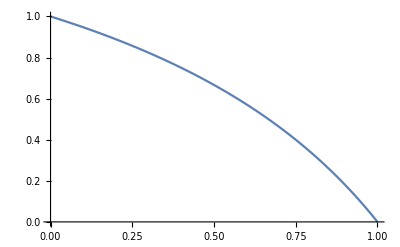

```mathematica
Plot[{4(1-p)/(2(2-p))},{p,0,1}]
```

```mathematica
combinedLike=p^lineIntecept(1-p)^lineClean(1-(1-p)^entrysize)^entriesIntercept((1-p)^entrysize)^entriesClean
combinedLogLike=Log[combinedLike]
FIMCombined=-D[D[combinedLogLike,p]//FullSimplify,p]//FullSimplify
SECombined=Sqrt[1/FIMCombined]/.lineClean->numLine*(1-p)/.lineIntecept-> numLine*p/.entriesClean->numEntries*(1-p)^entrysize/.entriesIntercept-> numEntries*(1-(1-p)^entrysize)//FullSimplify
```

(1-(1-p)^entrysize)^entriesIntercept (1-p)^lineClean ((1-p)^entrysize)^entriesClean p^lineIntecept

Log[(1-(1-p)^entrysize)^entriesIntercept (1-p)^lineClean ((1-p)^entrysize)^entriesClean p^lineIntecept]

(entriesIntercept entrysize (-1+entrysize+(1-p)^entrysize) (1-p)^(-2+entrysize))/((-1+(1-p)^entrysize)^2)+(entriesClean entrysize+lineClean)/(-1+p)^2+lineIntecept/p^2

√(-((-1+(1-p)^entrysize) (-1+p)^2 p)/(numLine-numLine p+(1-p)^entrysize (numLine (-1+p)+entrysize^2 numEntries p)))

```mathematica
FIMCombined/.lineClean->numLine*(1-p)/.lineIntecept-> numLine*p/.entriesClean->numEntries*(1-p)^entrysize/.entriesIntercept-> numEntries*(1-(1-p)^entrysize)//FullSimplify//Together
```

-((numLine-numLine (1-p)^entrysize-numLine p+entrysize^2 numEntries (1-p)^entrysize p+numLine (1-p)^entrysize p)/((-1+(1-p)^entrysize) (-1+p)^2 p))

```mathematica
SECombined/.p->0.05/.numLine->500/.numEntries->0/.entrysize->3
```

0.00974679

```mathematica
numLine (-2+p)+4 numEntries (-1+p)/.numEntries->0
```

numLine (-2+p)

```mathematica
SECombined/.entrysize->1//FullSimplify
SECombined/.entrysize->2//FullSimplify
SECombined/.entrysize->3//FullSimplify
SECombined/.entrysize->4//FullSimplify
SECombined/.entrysize->5//FullSimplify
SECombined/.entrysize->6//FullSimplify
SECombined/.entrysize->8//FullSimplify
```

√(-((-1+p) p)/(numEntries+numLine))

√(-((-2+p) (-1+p) p)/(numLine (-2+p)+4 numEntries (-1+p)))

√(-((-1+p) p (3+(-3+p) p))/(9 numEntries (-1+p)^2+numLine (3+(-3+p) p)))

√(-((-1+(-1+p)^4) (-1+p)^2 p)/(numLine-numLine p+(-1+p)^4 (numLine (-1+p)+16 numEntries p)))

√(-((-1+(1-p)^5) (-1+p)^2 p)/(numLine-numLine p+(1-p)^5 (numLine (-1+p)+25 numEntries p)))

√(-((-1+(-1+p)^6) (-1+p)^2 p)/(numLine-numLine p+(-1+p)^6 (numLine (-1+p)+36 numEntries p)))

√(-((-1+(-1+p)^8) (-1+p)^2 p)/(numLine-numLine p+(-1+p)^8 (numLine (-1+p)+64 numEntries p)))

```mathematica
Collect[9 numEntries (-1+p)^2+numLine (3+(-3+p) p),numLine]
Collect[numLine-numLine p+(-1+p)^4 (numLine (-1+p)+16 numEntries p),numLine]
Collect[numLine-numLine p+(1-p)^5 (numLine (-1+p)+25 numEntries p),numLine]
Collect[numLine-numLine p+(-1+p)^6 (numLine (-1+p)+36 numEntries p),numLine]
Collect[numLine-numLine p+(-1+p)^8 (numLine (-1+p)+64 numEntries p),numLine]
```

9 numEntries (-1+p)^2+numLine (3+(-3+p) p)

numLine (1+(-1+p)^5-p)+16 numEntries (-1+p)^4 p

numLine (1+(1-p)^5 (-1+p)-p)+25 numEntries (1-p)^5 p

numLine (1+(-1+p)^7-p)+36 numEntries (-1+p)^6 p

numLine (1+(-1+p)^9-p)+64 numEntries (-1+p)^8 p

```mathematica
(1-(1-p)^(entrysize+1)-p)/.entrysize->4//FullSimplify
```

1+(-1+p)^5-p

```mathematica
entrysize^2(1-p)^entrysize p/.entrysize->4//FullSimplify
```

16 (-1+p)^4 p

numLine (1+(-1+p)^5-p)+16 numEntries (-1+p)^4 p

numLine (1+(1-p)^5 (-1+p)-p)+25 numEntries (1-p)^5 p

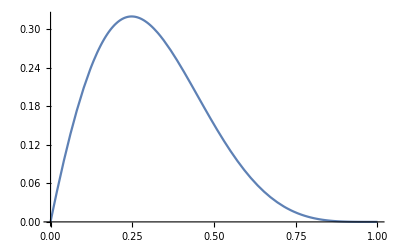

```mathematica
Plot[{25p(1-p)^5 /(5(1+(1-p)^5 (-1+p)-p))},{p,0,1}]
```

```mathematica
entrysize^2(1-p)^entrysize p/(entrysize(1-(1-p)^(entrysize+1)-p))//FullSimplify
```

-(entrysize (1-p)^(-1+entrysize) p)/(-1+(1-p)^entrysize)

```mathematica
Limit[(entrysize (1-p)^(-1+entrysize) p)/(-1+(1-p)^entrysize),{p->0}]
```

-1

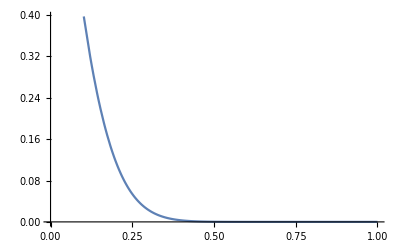

```mathematica
Plot[{-(entrysize (1-p)^(-1+entrysize) p)/(-1+(1-p)^entrysize)}/.entrysize->16,{p,0,1}]
```

```mathematica
D[-(entrysize (1-p)^(-1+entrysize) p)/(-1+(1-p)^entrysize)/.entrysize->6,p]
```

-(6 (1-p)^5)/(-1+(1-p)^6)+(30 (1-p)^4 p)/(-1+(1-p)^6)-(36 (1-p)^10 p)/((-1+(1-p)^6)^2)

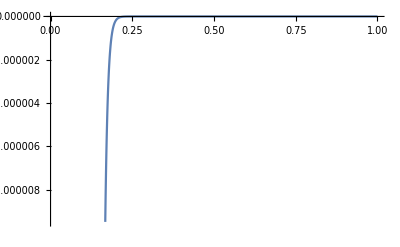

```mathematica
Plot[D[-(entrysize (1-p)^(-1+entrysize) p)/(-1+(1-p)^entrysize)/.entrysize->106,p]/.p->p2,{p2,0,1}]
```

```mathematica
D[D[(1-x)^n Log[(1-x)^n],x],x]//FullSimplify
```

n (1-x)^(-2+n) (-1+2 n+(-1+n) Log[(1-x)^n])

```mathematica
generalContainerLike = (1-(1-p)^entrysize)^entriesIntercept((1-p)^entrysize)^(entriesTotal-entriesIntercept)
generalContainerLogLike=Log[generalContainerLike]
FIMgeneralContainer=-D[D[generalContainerLogLike,p]//FullSimplify,p]//FullSimplify
FIMgeneralContainer/.entriesIntercept-> entriesTotal*(1-(1-p)^entrysize)//FullSimplify
SECombined=Sqrt[1/FIMgeneralContainer]/.entriesIntercept-> entriesTotal*(1-(1-p)^entrysize)//FullSimplify
```

(1-(1-p)^entrysize)^entriesIntercept ((1-p)^entrysize)^(-entriesIntercept+entriesTotal)

Log[(1-(1-p)^entrysize)^entriesIntercept ((1-p)^entrysize)^(-entriesIntercept+entriesTotal)]

(entrysize (entriesTotal+(entriesIntercept (-1+(1+entrysize) (1-p)^entrysize))/((-1+(1-p)^entrysize)^2)))/(-1+p)^2

-(entriesTotal entrysize^2 (1-p)^(-2+entrysize))/(-1+(1-p)^entrysize)

√(-((-1+(1-p)^entrysize) (1-p)^(2-entrysize))/(entriesTotal entrysize^2))

```mathematica
Manipulate[Plot[{-(entrysize^2 (1-p)^(-2+entrysize))/(-1+(1-p)^entrysize),-(1-p)^(-2+1)/(-1+(1-p)^1)entrysize},{entrysize,1,10},PlotRange->All],{p,.0001,.99999}]
```

```mathematica
(-(entrysize^2 (1-p)^(-2+entrysize))/(-1+(1-p)^entrysize))/(-(1-p)^(-2+1)/(-1+(1-p)^1)entrysize)//FullSimplify
```

-(entrysize (1-p)^(-1+entrysize) p)/(-1+(1-p)^entrysize)

```mathematica
Manipulate[Plot[{-(entrysize (1-p)^(-1+entrysize) p)/(-1+(1-p)^entrysize)},{entrysize,1,10},PlotRange->All],{p,.0001,.99999}]
```

```mathematica
D[-(entriesTotal entrysize^2 (1-p)^(-2+entrysize))/(-1+(1-p)^entrysize), entrysize]/.entriesTotal->1//FullSimplify
```

-(entrysize (1-p)^(-2+entrysize) (-2+2 (1-p)^entrysize-entrysize Log[1-p]))/((-1+(1-p)^entrysize)^2)

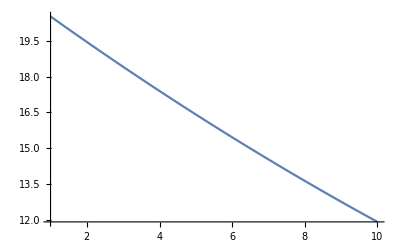

```mathematica
Plot[-(entrysize (1-p)^(-2+entrysize) (-2+2 (1-p)^entrysize-entrysize Log[1-p]))/((-1+(1-p)^entrysize)^2)/.p->.05,{entrysize,1,10}]
```

```mathematica
D[generalContainerLogLike,p]
```

(1-(1-p)^entrysize)^-entriesIntercept (-(-entriesIntercept+entriesTotal) entrysize (1-(1-p)^entrysize)^entriesIntercept (1-p)^(-1+entrysize) ((1-p)^entrysize)^(-1-entriesIntercept+entriesTotal)+entriesIntercept entrysize (1-(1-p)^entrysize)^(-1+entriesIntercept) (1-p)^(-1+entrysize) ((1-p)^entrysize)^(-entriesIntercept+entriesTotal)) ((1-p)^entrysize)^(entriesIntercept-entriesTotal)

```mathematica
Sqrt[1/((n s^2(1-p)^(s-2))/((1-p)^s-1))]
```

√(((-1+(1-p)^s) (1-p)^(2-s))/(n s^2))

```mathematica
Limit[(n s^2(1-p)^(s-2))/((1-p)^s-1),p-> 0]
```

Indeterminate

```mathematica
D[(n s^2(1-p)^(s-2))/((1-p)^s-1),p]//FullSimplify
```

(n (1-p)^(-3+s) s^2 (-2+2 (1-p)^s+s))/((-1+(1-p)^s)^2)

```mathematica
Limit[(n (1-p)^(-3+s) s^2 (-2+2 (1-p)^s+s))/((-1+(1-p)^s)^2),p-> 0]
```

n s^2 DirectedInfinity[1/Sign[s]]

```mathematica
(n s^2(1-p)^(s-2))/((1-p)^s-1)/.s->1
```

-n/((1-p) p)